```mathematica
csv=Import["~/Result_5.csv"];
```

```mathematica
data=#[[2]]&/@csv;
```

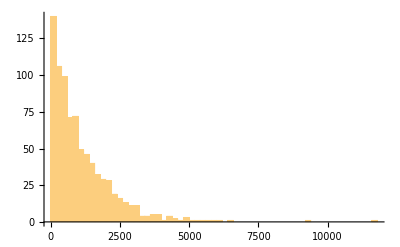

```mathematica
Histogram[data,50,PlotRange->All]
```

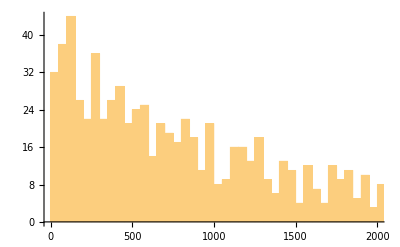

```mathematica
Histogram[data,300,PlotRange->{{0,2000},Automatic}]
```

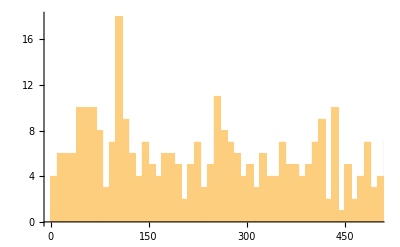

```mathematica
Histogram[data,800,PlotRange->{{0,500},Automatic}]
```